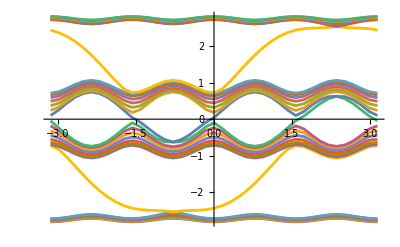

```mathematica
n=30;
alpha=3/4;
H[k_]:=N[Table[2*Cos[k+2*Pi*i*alpha]*KroneckerDelta[i,j]+KroneckerDelta[i+1,j]+KroneckerDelta[j+1,i],{i,1,n},{j,1,n}]];
ListLinePlot[Table[Table[{k,Sort[Eigenvalues[H[k]]][[i]]},{k,-Pi,Pi,Pi/20}],{i,1,n}]]
```